```mathematica
SetDirectory[NotebookDirectory[]];
```

### Definitions

```mathematica
k0=kp Cosh[ηk];
kx=kp Cos[ϕk];
ky=kp Sin[ϕk];
kz=kp Sinh[ηk];
kplus=FullSimplify[k0-kz];
kminus=FullSimplify[k0+kz];

ϕg=0;
kgx=kg0 Sin[θg]Cos[ϕg];
kgy=kg0 Sin[θg]Sin[ϕg];
kgz=kg0 Cos[θg];
kgplus=FullSimplify[kg0-kgz];
kgminus=FullSimplify[kg0+kgz];

g0=1;
gx=Sin[θg]Cos[ϕg];
gy=Sin[θg]Sin[ϕg];
gz=Cos[θg];
gplus=FullSimplify[g0-gz];
gminus=FullSimplify[g0+gz];
```

```mathematica
k3vec={kx,ky,kz};
kg3vec={kgx,kgy,kgz};
g3vec={gx,gy,gz};
```

### Simplifications

#### Phase space

```mathematica
FullSimplify[kplus-(k0 g0-k3vec.g3vec)]
```

kp Cos[ϕk] Sin[θg]+kp (-1+Cos[θg]) Sinh[ηk]

```mathematica
FullSimplify[-kp^2-kz^2]
```

-kp^2 Cosh[ηk]^2

#### Matrix element

```mathematica
m1=FullSimplify[2/(kplus kminus)]
```

2/kp^2

#### Measurement function

```mathematica
FullSimplify[(k0 g0-k3vec.g3vec)]
```

kp (Cosh[ηk]-Cos[ϕk] Sin[θg]-Cos[θg] Sinh[ηk])

```mathematica
FullSimplify[(kplus-(k0 g0-k3vec.g3vec))/kp]
```

Cos[ϕk] Sin[θg]+(-1+Cos[θg]) Sinh[ηk]

```mathematica
FullSimplify[Sin[x]/(1-Cos[x])]
```

Cot[x/2]

```mathematica
FullSimplify[(-kplus+(k0 g0-k3vec.g3vec))/kp]
```

-Cos[ϕk] Sin[θg]+Sinh[ηk]-Cos[θg] Sinh[ηk]

#### Soft drop groomer

```mathematica
FullSimplify[kplus-k0 gplus]
```

kp (Cos[θg] Cosh[ηk]-Sinh[ηk])

```mathematica
FullSimplify[(k0 g0-k3vec.g3vec)-k0 gplus]
```

kp (ⅇ^-ηk Cos[θg]-Cos[ϕk] Sin[θg])

#### Jacobian

```mathematica
FullSimplify[Det[({{1, 0, 0, 0}, {0, Cos[ϕk], -kp Sin[ϕk], 0}, {0, Sin[ϕk], kp Cos[ϕk], 0}, {0, Sinh[ηk], 0, kp Cosh[ηk]}})]]
```

kp^2 Cosh[ηk]

## Integration

```mathematica
Assuming[{ρ>0,μ>0},FullSimplify[Series[μ^(2ϵ)/Gamma[1-ϵ](Q/4)^(-2ϵ)1/ρ^(1+2ϵ),{ϵ,0,1}]/.EulerGamma->0]]
```

1/ρ-(2 Log[(Q ρ)/(4 μ)] ϵ)/ρ+O[ϵ]^2

```mathematica
Integrate[Sin[ϕ]^(-2ϵ),{ϕ,0,Pi}]
```

ConditionalExpression[(√π Gamma[1/2-ϵ])/Gamma[1-ϵ], 0<Re[ϵ]<1/2]

```mathematica
Series[Exp[-2ϵ η],{ϵ,0,1}]
```

1-2 η ϵ+O[ϵ]^2

```mathematica
Integrate[Exp[-2ϵ η],{η,a,Infinity}]
```

ConditionalExpression[ⅇ^(-2 a ϵ)/(2 ϵ), Re[ϵ]>0]

```mathematica
Series[Exp[-2ϵ η],{ϵ,0,1}]
```

1-2 η ϵ+O[ϵ]^2

```mathematica
Series[(Exp[η]/(Cosh[η]-Cos[ϕ]Sin[θ]-Sinh[η]Cos[θ]))^(-2ϵ),{ϵ,0,0}]
```

1+O[ϵ]^1

```mathematica
Integrate[Exp[-2ϵ η],{η,0,Infinity}]
```

ConditionalExpression[1/(2 ϵ), Re[ϵ]>0]

### Bounds in η

```mathematica
FullSimplify[Reduce[0<θ<Pi/2&&Cos[θ]>Tanh[η]&&η>0&&Cot[θ]>Exp[η]Cos[ϕ],η]]
```

θ>0&&2 θ<π&&η>0&&((η<Log[Cot[θ/2]]&&2 Cos[ϕ]+Tan[θ/2]^2<1)||(η<Log[Cot[θ] Sec[ϕ]]&&Cos[ϕ]<Cot[θ]&&2 Cos[ϕ]+Tan[θ/2]^2≥1))

```mathematica
FullSimplify[1/2 FullSimplify[1-Tan[θ/2]^2]]
```

1/(1+Sec[θ])

```mathematica
NIntegrate[Boole[1/(1+Sec[θ])>Cos[ϕ]]/.θ->Pi/3.,{ϕ,0,Pi}]
```

1.91063

```mathematica
NIntegrate[Boole[Sec[ϕ]>1+Sec[θ]]/.θ->Pi/3.,{ϕ,0,Pi/2}](*+NIntegrate[Boole[Sec[ϕ]<1+Sec[θ]]/.θ->Pi/3.,{ϕ,Pi/2,Pi}]*)+Pi/2
```

1.91063

```mathematica
NIntegrate[Boole[1/(1+Sec[θ])<Cos[ϕ]]/.θ->Pi/3.,{ϕ,0,Pi}]
```

1.23096

```mathematica
NIntegrate[Boole[Sec[ϕ]<1+Sec[θ]]/.θ->Pi/3.,{ϕ,0,Pi/2}]
```

1.23096

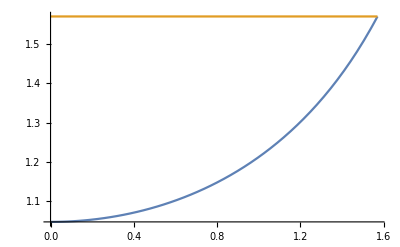

```mathematica
Plot[{ArcSec[1+Sec[θ]],Pi/2},{θ,0,Pi/2}]
```

### First part of the integral

```mathematica
NIntegrate[Boole[1/(1+Sec[θ])>Cos[ϕ]&&Cot[θ/2]>Exp[η]]/.θ->Pi/3.,{η,0,Infinity},{ϕ,0,Pi}]
```

1.04952

```mathematica
(Pi-ArcSec[1+Sec[θ]])Log[Cot[θ/2]]/.θ->Pi/3.
```

1.04952

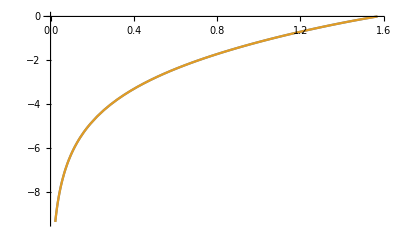

```mathematica
Plot[{-(Pi-ArcSec[1+Sec[θ]])Log[Cot[θ/2]],-NIntegrate[Boole[1/(1+Sec[θ])>Cos[ϕ]&&Cot[θ/2]>Exp[η]],{η,0,Infinity},{ϕ,0,Pi}]},{θ,0,Pi/2}]
```

### Second part of the integral

```mathematica
FullSimplify[1-1/Cot[θ]^2]
```

1-Tan[θ]^2

```mathematica
intval=Assuming[0<ϕ<Pi/2&&0<θ<Pi/2,FullSimplify[Integrate[Log[Cot[θ]Sec[ϕ]],ϕ]]]
```

1/2 (ϕ (ⅈ ϕ+Log[4]+2 Log[Cot[θ]])-ⅈ PolyLog[2,-ⅇ^(2 ⅈ ϕ)])

```mathematica
FullSimplify[Series[PolyLog[2,-ⅇ^(2 ⅈ ϕ)],{ϕ,0,8}]]
```

-π^2/12-2 ⅈ Log[2] ϕ+ϕ^2+(ⅈ ϕ^3)/3+(ⅈ ϕ^5)/30+(2 ⅈ ϕ^7)/315+O[ϕ]^9

```mathematica
ExpToTrig[Exp[2I k x]]
```

Cos[2 k x]+ⅈ Sin[2 k x]

```mathematica
TrigToExp[Cos[2 k x]]
```

1/2 ⅇ^(-2 ⅈ k x)+1/2 ⅇ^(2 ⅈ k x)

```mathematica
pl1=Sum[((-1)^k Cos[2k x])/k^2,{k,1,Infinity}]
```

1/2 (PolyLog[2,-ⅇ^(-2 ⅈ x)]+PolyLog[2,-ⅇ^(2 ⅈ x)])

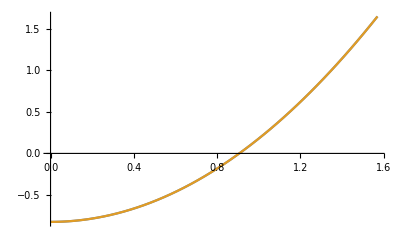

```mathematica
Plot[{pl1,x^2-Pi^2/12},{x,0,Pi/2}]
```

```mathematica
pl2=Sum[((-1)^k Sin[2k x])/k^2,{k,1,Infinity}]
```

```mathematica
1/2 ⅈ (PolyLog[2,-ⅇ^(-2 ⅈ x)]-PolyLog[2,-ⅇ^(2 ⅈ x)])
```

```mathematica
FullSimplify[ArcCos[1/(1+Sec[x])]]
```

ArcSec[1+Sec[x]]

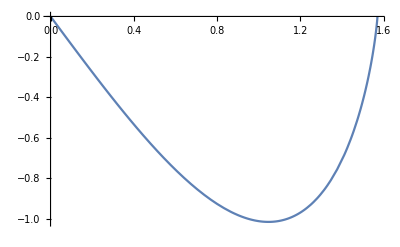

```mathematica
Plot[pl2,{x,0,Pi/2}]
```

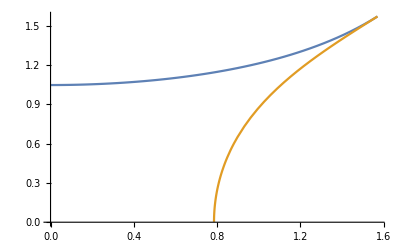

```mathematica
Plot[{ArcCos[1/(1+Sec[x])],ArcCos[Cot[x]]},{x,0, π/2},PlotRange->All]
```

```mathematica
FullSimplify[p1]
```

1/2 (ArcSec[1+Sec[θ]] (ⅈ ArcSec[1+Sec[θ]]+Log[4]+2 Log[Cot[θ]])-ⅈ PolyLog[2,ⅇ^(-2 ⅈ ArcCsc[1+Sec[θ]])])

```mathematica
FullSimplify[TrigToExp[-2 ⅈ ArcCsc[1+Sec[θ]]]]
```

-2 ⅈ ArcCsc[1+Sec[θ]]

```mathematica
p3=intval/.ϕ->0
```

(ⅈ π^2)/24

```mathematica
p2=intval/.ϕ->ArcCos[Cot[θ]]
```

1/2 (ArcCos[Cot[θ]] (ⅈ ArcCos[Cot[θ]]+Log[4]+2 Log[Cot[θ]])-ⅈ PolyLog[2,-ⅇ^(2 ⅈ ArcCos[Cot[θ]])])

```mathematica
p1-p2/.θ->Pi/3.
```

0.0670406+5.55112×10^-17 ⅈ

```mathematica
Assuming[0<θ<Pi/2,FullSimplify[p1-p2]]
```

```mathematica
-1/2 ⅈ ((ArcCsc[1+Sec[θ]]-ArcSin[Cot[θ]]) (ArcCos[Cot[θ]]+ArcSec[1+Sec[θ]]-ⅈ Log[4 Cot[θ]^2])+PolyLog[2,ⅇ^(-2 ⅈ ArcCsc[1+Sec[θ]])]-PolyLog[2,ⅇ^(-2 ⅈ ArcSin[Cot[θ]])])
```

```mathematica
p3=%256
```

-1/2 ⅈ ((ArcCsc[1+Sec[θ]]-ArcSin[Cot[θ]]) (ArcCos[Cot[θ]]+ArcSec[1+Sec[θ]]-ⅈ Log[4 Cot[θ]^2])+PolyLog[2,ⅇ^(-2 ⅈ ArcCsc[1+Sec[θ]])]-PolyLog[2,ⅇ^(-2 ⅈ ArcSin[Cot[θ]])])

```mathematica
p3/.θ->Pi/3.
```

0.0670406+5.55112×10^-17 ⅈ

```mathematica
p3/.θ->Pi/4.
```

0.294018-1.11022×10^-16 ⅈ

```mathematica
NIntegrate[Boole[Cos[ϕ]>1/(1+Sec[θ])&&Cot[θ]>Cos[ϕ]&&Cot[θ]Sec[ϕ]>Exp[η]]/.θ->Pi/3.,{η,0,Infinity},{ϕ,0,Pi}]
```

0.0670406

First polylogarithm

```mathematica
Simplify[TrigToExp[2 I ArcCsc[1+Sec[θ]]]]
```

2 Log[(ⅈ (1+ⅇ^(2 ⅈ θ)))/((1+ⅇ^(ⅈ θ))^2)+√(1-((1+ⅇ^(2 ⅈ θ))^2)/((1+ⅇ^(ⅈ θ))^4))]

```mathematica
FullSimplify[((ⅈ (1+ⅇ^(2 ⅈ θ)))/((1+ⅇ^(ⅈ θ))^2)+√(1-((1+ⅇ^(2 ⅈ θ))^2)/((1+ⅇ^(ⅈ θ))^4)))^2]
```

((ⅈ Cos[θ])/(1+Cos[θ])+1/2 √((1+2 Cos[θ]) Sec[θ/2]^4))^2

```mathematica
PolyLog[2,-((ⅈ Cos[θ])/(1+Cos[θ])+1/2 √((1+2 Cos[θ]) Sec[θ/2]^4))^2]/.θ->Pi/3.
```

-0.706978-0.457877 ⅈ

```mathematica
PolyLog[2,ⅇ^(-2 ⅈ ArcCsc[1+Sec[θ]])]/.θ->Pi/3.
```

0.692794-0.946496 ⅈ

Second polylogarithm

```mathematica
Simplify[TrigToExp[ArcSin[Cot[θ]]]]
```

-ⅈ Log[(1+ⅇ^(2 ⅈ θ))/(1-ⅇ^(2 ⅈ θ))+√2 √((1+ⅇ^(4 ⅈ θ))/((-1+ⅇ^(2 ⅈ θ))^2))]

```mathematica
FullSimplify[(1+ⅇ^(2 ⅈ θ))/(1-ⅇ^(2 ⅈ θ))+√2 √((1+ⅇ^(4 ⅈ θ))/((-1+ⅇ^(2 ⅈ θ))^2))]
```

ⅈ Cot[θ]+√(1-Cot[θ]^2)

Final answer for part 2 of the integral

```mathematica
intval=Integrate[Log[Cot[θ]Sec[x]],x]
```

-(ⅈ x^2)/2+x Log[1+ⅇ^(2 ⅈ x)]+x Log[Cot[θ] Sec[x]]-1/2 ⅈ PolyLog[2,-ⅇ^(2 ⅈ x)]

```mathematica
intvalMine[x_]:=x Log[2Cot[θ]]+I/4(PolyLog[2,-Exp[-2I x]]-PolyLog[2,-Exp[2I x]])+(I Pi^2)/24
```

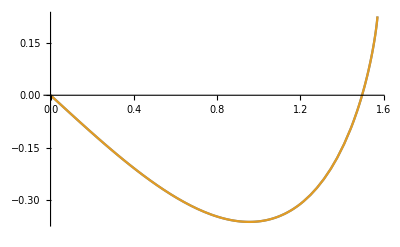

```mathematica
Plot[{Re[intval]/.θ->Pi/3.,Re[intvalMine[x]]/.θ->Pi/3.},{x,0,Pi/2}]
```

```mathematica
intFinal[x_]:=ArcSec[1+Sec[x]]Log[2Cot[x]]+I/4(PolyLog[2,-Exp[-2I ArcSec[1+Sec[x]]]]-PolyLog[2,-Exp[2I ArcSec[1+Sec[x]]]])-Boole[x>Pi/4](ArcCos[Cot[x]]Log[2Cot[x]]+I/4(PolyLog[2,-Exp[-2I ArcCos[Cot[x]]]]-PolyLog[2,-Exp[2I ArcCos[Cot[x]]]]))
```

```mathematica
intNumerics=Table[{θ,NIntegrate[Boole[Cos[ϕ]>1/(1+Sec[θ])&&Cot[θ]>Cos[ϕ]&&Cot[θ]Sec[ϕ]>Exp[η]],{ϕ,0,Pi},{η,0,Infinity}]},{θ,0.1,Pi/2,Pi/20.}]
```

{{0.1,2.63048},{0.25708,1.63704},{0.414159,1.11801},{0.571239,0.739223},{0.728319,0.410666},{0.885398,0.167902},{1.04248,0.0690088},{1.19956,0.0230307},{1.35664,0.00447298},{1.51372,0.0000898504}}

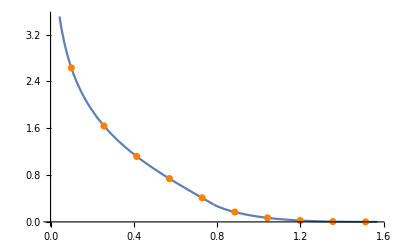

```mathematica
p1=Plot[intFinal[x],{x,0,Pi/2}];
p2=ListPlot[intNumerics,PlotStyle->Orange];
Show[p1,p2]
```

### Full non-divergent integral plot

```mathematica
fullNumerics=Table[{θ,NIntegrate[Boole[Cos[θ]>Tanh[η]&&Cot[θ]>Exp[η]Cos[ϕ]],{ϕ,0,Pi},{η,0,Infinity}]},{θ,0.1,Pi/2,Pi/30.}]
```

{{0.1,8.89865},{0.20472,6.6309},{0.30944,5.30401},{0.414159,4.34623},{0.518879,3.58166},{0.623599,2.93137},{0.728319,2.35167},{0.833038,1.84154},{0.937758,1.45363},{1.04248,1.13002},{1.1472,0.849813},{1.25192,0.602368},{1.35664,0.381498},{1.46136,0.183684},{1.56608,0.00743603}}

```mathematica
fullAnalytic[x_]:=(Pi-ArcSec[1+Sec[x]])Log[Cot[x/2]]+(ArcSec[1+Sec[x]]Log[2Cot[x]]+I/4(PolyLog[2,-Exp[-2I ArcSec[1+Sec[x]]]]-PolyLog[2,-Exp[2I ArcSec[1+Sec[x]]]])-Boole[x>Pi/4](ArcCos[Cot[x]]Log[2Cot[x]]+I/4(PolyLog[2,-Exp[-2I ArcCos[Cot[x]]]]-PolyLog[2,-Exp[2I ArcCos[Cot[x]]]])))
```

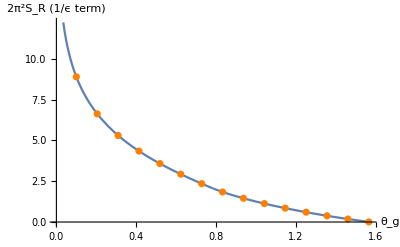

```mathematica
fullPlot1=Plot[fullAnalytic[x],{x,0,Pi/2}];
fullPlot2=ListPlot[fullNumerics,PlotStyle->Orange];
fullPlot=Show[fullPlot1,fullPlot2,AxesLabel->{"θ_g","2π^2S_R (1/ϵ term)"}]
```

```mathematica
Export["figures/full_non_divergent.pdf",fullPlot,"PDF"]
```

figures/full_non_divergent.pdf

### Full integral plot

```mathematica
Q=91.2; (*mass of Z boson in GeV*)
αs=0.118; (*value of αs at Z boson mass*)
CF=4/3;(*from PDG*)
μ=10.;
ϵ=0.0001;
ρs=0.1;
```

```mathematica
fullNumerics=Table[numVal=(*1/(2ϵ)(Sqrt[Pi] Gamma[1/2-ϵ] )/Gamma[1-ϵ]-*)NIntegrate[(2Pi αs CF μ^(2ϵ))/(Pi^(5/2)Gamma[1/2-ϵ])(Q/4)^(-2ϵ)1/ρs^(1+2ϵ)Sin[ϕ]^(-2ϵ)Exp[-2ϵ η](1-Boole[Cos[θ]>Tanh[η]&&Cot[θ]>Exp[η]Cos[ϕ]]),{ϕ,0,Pi},{η,0,Infinity},IntegrationMonitor:>((errors=Through[#1@"Error"])&)];{θ,numVal,Total@errors},{θ,0.1,Pi/2,Pi/30.}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.1,5006.43,0.00499569},{0.20472,5007.15,0.00497635},{0.30944,5007.58,0.00499395},{0.414159,5007.88,0.00499454},{0.518879,5008.12,0.00498052},{0.623599,5008.33,0.00498431},{0.728319,5008.5,0.00499591},{0.833038,5008.68,0.00500639},{0.937758,5008.8,0.00497815},{1.04248,5008.91,0.00499939},{1.1472,5009.,0.00500782},{1.25192,5009.07,0.0049643},{1.35664,5009.14,0.00500809},{1.46136,5009.21,0.00496559},{1.56608,5009.27,0.00498716}}

```mathematica
fullAnalytic[x_]:=(2Pi αs CF μ^(2ϵ))/(Pi^(5/2)Gamma[1/2-ϵ])(Q/4)^(-2ϵ)1/ρs^(1+2ϵ)(1/(2ϵ)(√Pi Gamma[1/2-ϵ])/Gamma[1-ϵ]-(Pi-ArcSec[1+Sec[x]])Log[Cot[x/2]]-ArcSec[1+Sec[x]]Log[2Cot[x]]-I/4(PolyLog[2,-Exp[-2I ArcSec[1+Sec[x]]]]-PolyLog[2,-Exp[2I ArcSec[1+Sec[x]]]])
+Boole[x>Pi/4]
(ArcCos[Cot[x]]Log[2Cot[x]]+I/4(PolyLog[2,-Exp[-2I ArcCos[Cot[x]]]]-PolyLog[2,-Exp[2I ArcCos[Cot[x]]]])))
```

```mathematica
numToPlot=Table[{fullNumerics[[i,1]],fullNumerics[[i,2]]},{i,1,Length[fullNumerics]}]
```

{{0.1,5006.43},{0.20472,5007.15},{0.30944,5007.58},{0.414159,5007.88},{0.518879,5008.12},{0.623599,5008.33},{0.728319,5008.5},{0.833038,5008.68},{0.937758,5008.8},{1.04248,5008.91},{1.1472,5009.},{1.25192,5009.07},{1.35664,5009.14},{1.46136,5009.21},{1.56608,5009.27}}

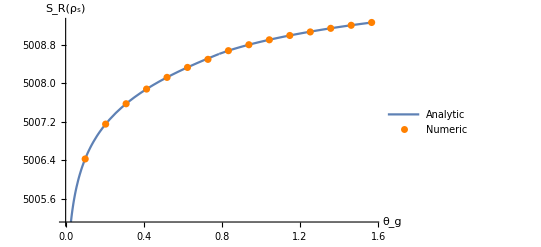

```mathematica
fullPlot1=Plot[Legended[fullAnalytic[x],"Analytic"],{x,0,Pi/2},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,FontColor->Black}];
fullPlot2=ListPlot[Legended[numToPlot,"Numeric"],PlotStyle->Orange,LabelStyle->{FontFamily->"CMU Serif",FontSize->14,FontColor->Black}];
fullPlot=Show[fullPlot1,fullPlot2, (*fullPlot3,*)AxesLabel->{"θ_g","S_R(ρ_s)"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,FontColor->Black}]
```

```mathematica
Export["figures/full_eps_0.0001.pdf",fullPlot,"PDF"]
```

figures/full_eps_0.0001.pdf

## Transformation

```mathematica
LaplaceTransform[1/ρ^(1+2ϵ),ρ,ν]
```

ν^(2 ϵ) Gamma[-2 ϵ]

## Expansion

```mathematica
Assuming[{Q>0,ν>0, μ>0},FullSimplify[Series[(2Pi)/(Pi^(5/2)Gamma[1/2-ϵ])(Q/(4μ ν))^(-2ϵ)Gamma[-2ϵ],{ϵ,0,1}]/.EulerGamma->0]/.EulerGamma->0]
```

-1/(π^2 ϵ)+Log[Q^2/(4 μ^2 ν^2)]/π^2+(-1/12-Log[4]^2/(2 π^2)-(2 Log[(μ ν)/Q] Log[(4 μ ν)/Q])/π^2) ϵ+O[ϵ]^2

```mathematica
Assuming[{x>0},FullSimplify[Series[(2Pi)/(Pi^(5/2)Gamma[1/2-ϵ])(x)^(-2ϵ)Gamma[-2ϵ],{ϵ,0,1}]/.EulerGamma->0]/.EulerGamma->0]
```

-1/(π^2 ϵ)+(Log[4]+2 Log[x])/π^2+(-1/12-Log[4]^2/(2 π^2)-(2 Log[x] (Log[4]+Log[x]))/π^2) ϵ+O[ϵ]^2

```mathematica
FullSimplify[Series[(√Pi Gamma[1/2-ϵ])/(2ϵ Gamma[1-ϵ]),{ϵ,0,0}]]
```

π/(2 ϵ)+π Log[2]+O[ϵ]^1

```mathematica
Series[((4 μ^2)/(z^2 Q^2))^(2ϵ),{ϵ,0,1}]
```

1+2 (Log[4]+Log[μ^2/(Q^2 z^2)]) ϵ+O[ϵ]^2

## Resummation

```mathematica
βfunc=-2a(β0 a/(4Pi)+β1 (a/(4Pi))^2+β2( a/(4Pi))^3+β3(a/(4Pi))^4)
Γfunc=Γ0 a/(4Pi)+Γ1 (a/(4Pi))^2+Γ2 (a/(4Pi))^3+Γ3(a/(4Pi))^4
γfunc=γ0 a/(4Pi)+γ1 (a/(4Pi))^2+γ2 (a/(4Pi))^3+γ3(a/(4Pi))^4
```

-2 a ((a β0)/(4 π)+(a^2 β1)/(16 π^2)+(a^3 β2)/(64 π^3)+(a^4 β3)/(256 π^4))

(a Γ0)/(4 π)+(a^2 Γ1)/(16 π^2)+(a^3 Γ2)/(64 π^3)+(a^4 Γ3)/(256 π^4)

(a γ0)/(4 π)+(a^2 γ1)/(16 π^2)+(a^3 γ2)/(64 π^3)+(a^4 γ3)/(256 π^4)

### First exponentiated integral

```mathematica
Series[1/βfunc,{a,0,-1}]
```

-(2 π)/(β0 a^2)+β1/(2 β0^2 a)+O[a]^0

```mathematica
Series[Γfunc/βfunc,{a,0,0}]
```

-Γ0/(2 β0 a)+(β1 Γ0-β0 Γ1)/(8 π β0^2)+O[a]^1

```mathematica
Integrate[Series[1/βfunc,{a,0,-1}],a]
```

(2 π)/(β0 a)+(β1 Log[a])/(2 β0^2)+O[a]^1

```mathematica
Series[4 β0^2/Γ0 Γfunc/βfunc Assuming[{aμ0>0},Integrate[Series[1/βfunc,{a,0,-1}],{a,aμ0,ap}]]/.ap->a,{a,0,-1}]
```

-(4 π)/a^2+(4 π β0 Γ0+aμ0 β1 Γ0-aμ0 β0 Γ1-aμ0 β1 Γ0 Log[a/aμ0])/(aμ0 β0 Γ0 a)+O[a]^0

```mathematica
Assuming[{aμ0>0,aμ>0,aμ≠aμ0},Integrate[β1/(β0 a)Log[a/aμ0],{a,aμ0,aμ}]]
```

(β1 Log[aμ/aμ0]^2)/(2 β0)

### Second exponentiated integrand

```mathematica
Series[γfunc/βfunc,{a,0,-1}]
```

-γ0/(2 β0 a)+O[a]^0

### Third exponentiated integral

```mathematica
Series[Γfunc/βfunc,{a,0,0}]
```

-Γ0/(2 β0 a)+(β1 Γ0-β0 Γ1)/(8 π β0^2)+O[a]^1

```mathematica
(2β0 /Γ0 )Assuming[{aμ0>0,aμ>0,aμ0≠aμ},Integrate[Series[Γfunc/βfunc,{a,0,0}],{a,aμ0,aμ}]]
```

((aμ-aμ0) (β1 Γ0-β0 Γ1)+4 π β0 Γ0 Log[aμ0/aμ])/(4 π β0 Γ0)

## Final touches

```mathematica
nf=5; (*number of quark flavors*)
Q=91.2; (*mass of Z boson in GeV*)
αs=0.118; (*value of αs at Z boson mass*)
b0=(33-2nf)/(12Pi);b1=(153-19nf)/(24Pi^2);(*from PDG*)
CF=4/3;(*from PDG*)

β0=11-(2nf)/3;β1=102-nf 19/24*16;
Γ0=4;Γ1=12(67/9-Pi^2/3)-40/9 nf;

θg=Pi/3.;
μ0=(Q ρ)/2;
Clear[μ]
```

Angular function

```mathematica
f[t_]:=Chop[Pi Log[2]-(Pi-ArcSec[1+Sec[t]])Log[Cot[t/2]]-ArcSec[1+Sec[t]]Log[2Cot[t]]-I/4(PolyLog[2,-Exp[-2I ArcSec[1+Sec[t]]]]-PolyLog[2,-Exp[2I ArcSec[1+Sec[t]]]])+HeavisideTheta[t-Pi/4](ArcCos[Cot[t]]Log[2Cot[t]]+I/4(PolyLog[2,-Exp[-2I ArcCos[Cot[t]]]]-PolyLog[2,-Exp[2I ArcCos[Cot[t]]]]))];
```

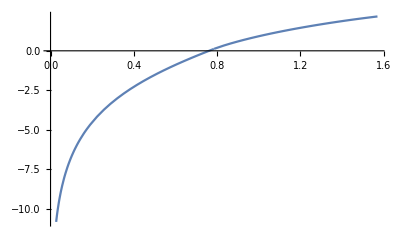

```mathematica
Plot[f[t],{t,0,Pi/2}]
```

Running coupling

```mathematica
s=NDSolve[{μ D[α[μ],μ]==-b0 α[μ]^2-b1 α[μ]^3,α[91.2]==0.118},α,{μ,1,1000000000}];
αnum[μ_]=(α[μ]/.s)[[1]];
```

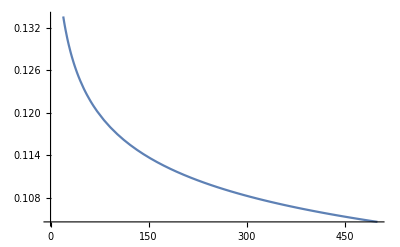

```mathematica
Plot[Evaluate[α[μ]/.s],{μ,0,500}]
```

```mathematica
r[μ_,μ0_]:=αnum[μ]/αnum[μ0];
```

```mathematica
K[ρ_,μ_,μ0_]:=-(CF Γ0)/(4β0^2)((4Pi)/αnum[μ0](Log[1/r[μ,μ0]]+1/r[μ,μ0]-1)+Log[r[μ,μ0]](β1/β0-Γ1/Γ0)+β1^2/(2β0)Log[r[μ,μ0]]^2)+(2CF)/(Pi β0)f[θg] Log[r[μ,μ0]];
```

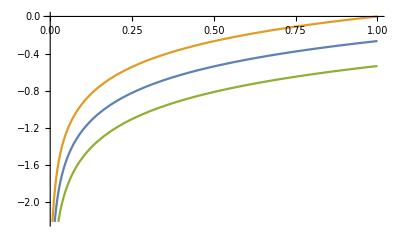

```mathematica
Plot[{K[ρ,Q,μ0],K[ρ,Q/2,μ0],K[ρ,2Q,μ0]},{ρ,0.001,1}]
```

```mathematica
ω[ρ_,μ_,μ0_]:=(-CF Γ0)/(4β0)(Log[1/r[μ,μ0]]+αnum[μ0]/(4Pi)(r[μ,μ0]-1)(β1/β0-Γ1/Γ0));
```

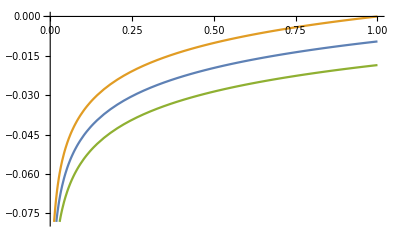

```mathematica
Plot[{ω[ρ,Q,μ0],ω[ρ,Q/2,μ0],ω[ρ,2Q,μ0]},{ρ,0.001,1}]
```

```mathematica
p1[ρ_,μ_,μ0_]:=FullSimplify[(αnum[μ0] CF)/(4Pi)(8 f[θg])/Pi 1/ρ D[((4 μval^2)/(Q^2 ρ^2))^w 1/Gamma[-2w],w]/.{w->ω[ρ,μ,μ0],μval->μ0}]
p2[ρ_,μ_,μ0_]:=FullSimplify[(αnum[μ0] CF)/(4Pi)4/ρ D[((4μval^2)/(Q^2 ρ^2))^w 1/Gamma[-2w],{w,2}]/.{w->ω[ρ,μ,μ0],μval->μ0}]
```

```mathematica
SR[ρ_,μ_,μ0_]:=Exp[K[ρ,μ,μ0]](1/ρ 1/Gamma[-2ω[ρ,μ,μ0]]+p1[ρ,μ,μ0]+p2[ρ,μ,μ0])
```

Comparison plot

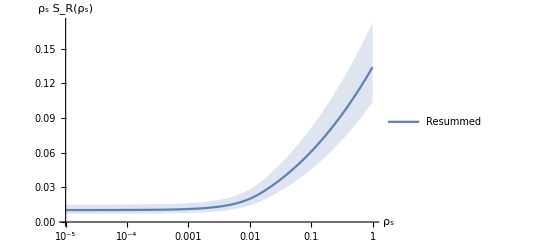

```mathematica
plot=LogLinearPlot[{Legended[ρ SR[ρ,Q,μ0],"Resummed"],(*Legended[ρ SRfirstOrder[Q,ρ,θg],"First-order"]*),ρ SR[ρ,2Q,μ0],ρ SR[ρ,Q/2,μ0]},{ρ,10^-5,1}, AxesLabel->{"ρ_s", "ρ_s S_R(ρ_s)"},Filling->{1->{3},1->{4}},PlotStyle->{Automatic,Automatic,None,None},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,FontColor->Black}]
```

```mathematica
Export["figures/resummation_plot.pdf",plot,"PDF"]
```

figures/resummation_plot.pdf

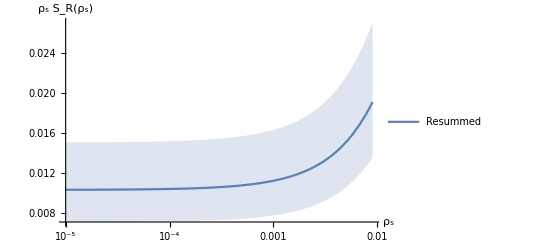

```mathematica
plot2=LogLinearPlot[{Legended[ρ SR[ρ,Q,μ0],"Resummed"],(*Legended[ρ SRfirstOrder[Q,ρ,θg],"First-order"]*),ρ SR[ρ,2Q,μ0],ρ SR[ρ,Q/2,μ0]},{ρ,10^-5,0.009}, AxesLabel->{"ρ_s", "ρ_s S_R(ρ_s)"},Filling->{1->{3},1->{4}},PlotStyle->{Automatic,Automatic,None,None},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,FontColor->Black}]
```

```mathematica
Export["figures/resummation_plot_zoomed.pdf",plot2,"PDF"]
```

figures/resummation_plot_zoomed.pdf

### Try to ignore non-cusp anomalous dimension and turn off running coupling

```mathematica
s1=Series[(-2Pi α Cf μ^(2ϵ))/(Pi^(5/2)Gamma[1/2-ϵ])(q/4)^(-2ϵ)1/ρ^(1+2ϵ),{ϵ,0,1}]/.EulerGamma->0
```

-(2 (Cf α))/(π^2 ρ)-(2 (Cf α (4 Log[2]-2 Log[q]+2 Log[μ]-2 Log[ρ]+PolyGamma[0,1/2])) ϵ)/(π^2 ρ)+O[ϵ]^2

```mathematica
s2=Series[1/(2ϵ)(√Pi Gamma[1/2-ϵ])/Gamma[1-ϵ],{ϵ,0,1}]/.EulerGamma->0
```

π/(2 ϵ)-1/2 π PolyGamma[0,1/2]+1/12 √π (π^(5/2)+3 √π PolyGamma[0,1/2]^2) ϵ+O[ϵ]^2

```mathematica
s1*s2
```

-(Cf α)/(π ρ ϵ)+((Cf α PolyGamma[0,1/2])/(π ρ)-(Cf α (4 Log[2]-2 Log[q]+2 Log[μ]-2 Log[ρ]+PolyGamma[0,1/2]))/(π ρ))+O[ϵ]^1

```mathematica
Series[(-2Pi α Cf μ^(2ϵ))/(Pi^(5/2)Gamma[1/2-ϵ])(q/4)^(-2ϵ)1/ρ^(1+2ϵ)(1/(2ϵ)Gamma[1/2-ϵ]/(Pi^(5/2)Gamma[1-ϵ])+g[θ]),{ϵ,0,0}]/.EulerGamma->0
```

-(Cf α)/(π^4 ρ ϵ)-(Cf α (2 π^2 g[θ]+4 Log[2]-2 Log[q]+2 Log[μ]-2 Log[ρ]))/(π^4 ρ)+O[ϵ]^1

```mathematica
SRfirstOrderTest[μ_,ρ_]:=(4CF αs)/(Pi ρ)Log[(2μ)/(Q ρ)];
```

```mathematica
D[x^w 1/Gamma[-2w],w]
```

(x^w Log[x])/Gamma[-2 w]+(2 x^w PolyGamma[0,-2 w])/Gamma[-2 w]

```mathematica
Limit[D[x^w 1/Gamma[-2w],{w,2}],w->0]/.EulerGamma->0
```

-4 Log[x]

```mathematica
SRTest[μ_,ρ_,μ0_]:=InverseLaplaceTransform[(1+(αs CF)/(4Pi)(8/Pi Log[(2μ ν)/Q]f[θg]+4Log[(2μ0 ν)/Q]^2))
Exp[CF/2 αs/Pi(Log[μ]^2/2-Log[Q/(2ν)]Log[μ])],ν,ρ]
```

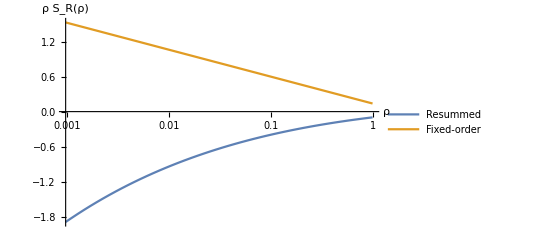

```mathematica
plotTest=LogLinearPlot[{Legended[ρ SRTest[Q,ρ,Q],"Resummed"],Legended[ρ SRfirstOrderTest[Q ,ρ],"Fixed-order"]},{ρ,0,1},AxesLabel->{"ρ","ρ S_R(ρ)"}]
```

```mathematica
Export["figures/resummation_plot_no_running_coupling.pdf",plotTest,"PDF"]
```

figures/resummation_plot_no_running_coupling.pdf

## Part 2

### First integral

```mathematica
Integrate[Exp[x-2ϵ x]/(Cosh[x]-A-B Sinh[x]),x]
```

∫ⅇ^(x-2 x ϵ)/(-A+Cosh[x]-B Sinh[x])ⅆx

```mathematica
Simplify[TrigToExp[Exp[x]/(Cosh[x]-B Sinh[x]-A)]]
```

(2 ⅇ^(2 x))/(1+B-2 A ⅇ^x+ⅇ^(2 x)-B ⅇ^(2 x))

```mathematica
Integrate[Exp[2x-2ϵ x]/(1+B-A Exp[x]+(1-B) Exp[2x]),x]
```

∫ⅇ^(2 x-2 x ϵ)/(1+B-A ⅇ^x+(1-B) ⅇ^(2 x))ⅆx

```mathematica
Assuming[0<ϵ<1/2,Integrate[u^(1-2ϵ)/(1+B-2A u+(1-B)u^2),u]]
```

-((u^(2-2 ϵ) ((A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,((-1+B) u)/(-A+√(-1+A^2+B^2))]+(-A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,(u-B u)/(A+√(-1+A^2+B^2))]))/(4 (1+B) √(-1+A^2+B^2) (-1+ϵ)))

Upper bound

```mathematica
Assuming[0<ϵ<1/2,Limit[-((u^(2-2 ϵ) ((A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,((-1+B) u)/(-A+√(-1+A^2+B^2))]+(-A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,(u-B u)/(A+√(-1+A^2+B^2))]))/(4 (1+B) √(-1+A^2+B^2) (-1+ϵ))),u->Infinity]]
```

-(((2 A^2 ((-1+B)/(A+√(-1+A^2+B^2)))^(2 ϵ)+2 A √(-1+A^2+B^2) ((-1+B)/(A+√(-1+A^2+B^2)))^(2 ϵ)+(-1+B^2) (((-1+B)/(A+√(-1+A^2+B^2)))^(2 ϵ)+(-(A+√(-1+A^2+B^2))/(1+B))^(2 ϵ))) Gamma[3-2 ϵ] Gamma[-1+2 ϵ])/(4 (-1+B) √(-1+A^2+B^2) (A+√(-1+A^2+B^2)) (-1+ϵ)))

Lower bound

```mathematica
-((u^(2-2 ϵ) ((A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,((-1+B) u)/(-A+√(-1+A^2+B^2))]+(-A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,(u-B u)/(A+√(-1+A^2+B^2))]))/(4 (1+B) √(-1+A^2+B^2) (-1+ϵ)))/.u->1
```

-(((A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,(-1+B)/(-A+√(-1+A^2+B^2))]+(-A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,(1-B)/(A+√(-1+A^2+B^2))])/(4 (1+B) √(-1+A^2+B^2) (-1+ϵ)))

Full integral value

```mathematica
intVal=FullSimplify[-(((2 A^2 ((-1+B)/(A+√(-1+A^2+B^2)))^(2 ϵ)+2 A √(-1+A^2+B^2) ((-1+B)/(A+√(-1+A^2+B^2)))^(2 ϵ)+(-1+B^2) (((-1+B)/(A+√(-1+A^2+B^2)))^(2 ϵ)+(-(A+√(-1+A^2+B^2))/(1+B))^(2 ϵ))) Gamma[3-2 ϵ] Gamma[-1+2 ϵ])/(4 (-1+B) √(-1+A^2+B^2) (A+√(-1+A^2+B^2)) (-1+ϵ)))+-(((A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,(-1+B)/(-A+√(-1+A^2+B^2))]+(-A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,(1-B)/(A+√(-1+A^2+B^2))])/(4 (1+B) √(-1+A^2+B^2) (-1+ϵ)))]
```

1/(4 √(-1+A^2+B^2) (-1+ϵ))((2 (-2 A √(-1+A^2+B^2) ((-1+B)/(A+√(-1+A^2+B^2)))^(2 ϵ)-(-1+2 A^2+B^2) ((-1+B)/(A+√(-1+A^2+B^2)))^(2 ϵ)-(-1+B^2) (-(A+√(-1+A^2+B^2))/(1+B))^(2 ϵ)) π (-1+ϵ) Csc[2 π ϵ])/((-1+B) (A+√(-1+A^2+B^2)))-1/(1+B)((-A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,(1-B)/(A+√(-1+A^2+B^2))]+(A+√(-1+A^2+B^2)) Hypergeometric2F1[1,2-2 ϵ,3-2 ϵ,(A+√(-1+A^2+B^2))/(1+B)]))

```mathematica
intValTrue=FullSimplify[intVal/.{A->Cos[ϕ]Sin[θ],B->Cos[θ]}]
```

(Gamma[2-2 ϵ] (Hypergeometric2F1Regularized[1,2-2 ϵ,3-2 ϵ,(1-Cos[θ])/(Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2))] (-Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2))+Hypergeometric2F1Regularized[1,2-2 ϵ,3-2 ϵ,(Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2))/(1+Cos[θ])] (Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2)))+(π (1+Cos[θ])^2 Csc[2 π ϵ] Csc[θ] (-(-(Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2))/(1+Cos[θ]))^(2 ϵ)+((-1+Cos[θ])/(Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2)))^(2 ϵ) (Cos[2 ϕ]+2 Cos[ϕ] Csc[θ] √(-Sin[θ]^2 Sin[ϕ]^2))))/(Cos[ϕ]+Csc[θ] √(-Sin[θ]^2 Sin[ϕ]^2)))/(2 (1+Cos[θ]) √(-Sin[θ]^2 Sin[ϕ]^2))

```mathematica
FullSimplify[Series[intValTrue,{ϵ,0,0}]]
```

1/((2-2 Cos[θ]) ϵ)+(-(((1+Cos[θ]) ((1+Cos[θ]) Log[1-(Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2))/(1+Cos[θ])]+Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2)))/(Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2)))+1/(-1+Cos[θ])^2 Sin[θ]^2 (1-Cos[θ]+Log[1+(-1+Cos[θ])/(Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2))] (Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2)))+((1+Cos[θ])^2 Csc[θ] (-Log[-(Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2))/(1+Cos[θ])]+Log[(-1+Cos[θ])/(Cos[ϕ] Sin[θ]+√(-Sin[θ]^2 Sin[ϕ]^2))] (Cos[2 ϕ]+2 Cos[ϕ] Csc[θ] √(-Sin[θ]^2 Sin[ϕ]^2))))/(Cos[ϕ]+Csc[θ] √(-Sin[θ]^2 Sin[ϕ]^2)))/(2 (1+Cos[θ]) √(-Sin[θ]^2 Sin[ϕ]^2))+O[ϵ]^1

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {2.40385}. NIntegrate obtained 68243. and 12565.3 for the integral and error estimates.

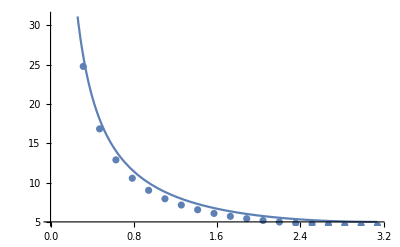

```mathematica
epsVal=1/5.;thetaVal=Pi/4.;
num=Table[{ϕ,NIntegrate[(u^(1-2ϵ)/(1+B-2A u+(1-B)u^2)/.{A->Cos[ϕ]Sin[θ],B->Cos[θ]})/.{ϵ->epsVal,θ->thetaVal},{u,1,Infinity}]},{ϕ,0,Pi,Pi/20.}];
p1=Plot[(intVal/.{A->Cos[ϕ]Sin[θ],B->Cos[θ]})/.{ϵ->epsVal,θ->thetaVal},{ϕ,0,Pi}];
p2=ListPlot[num];
Show[p1,p2]
```